# MMA Notes

2023.09.04

## MMA cheat sheet

## Information

?symbol (Show information of that symbol)

??symbol (Show more detailed information of that symbol)

?*symbol* (Show information of that symbol with regex. e.g. ?*Q)

## operator

+ (Plus), - (Subtract), * (Times), / (Divide), ^ (Power), += , -=, *=, /=

> (Greater), != (Unequal), && (And), <= (LessEqual), || (Or), == (Equal, equal of value after evaluation)

=== (SameQ, equal of the whole expression),  =!= (UnsameQ)

## Results

% (the last result)

%% (n % means the output of last n runs), equals %n or Out[n]

## Assignment

lhs = rhs (Set, assign the evaluation result of rhs to lhs instantaneously)

lhs := rhs (SetDelayed, assign the evaluation result of rhs to lhs whenever the lhs is utilized)

## List

{a, b, c,{d,e}} (A list is defined in {})

Level[list, {level_you_want_to_Part}] (Return the list in the corresponding level. Level 0 means the whole list or the entire expression. Level 1 removes one layer from the top of the tree form.)

Position[list, element] (Return the position of the element in a list.)

MapAt[function, list, position] (Map the function on the specified position.)

MapThread (Map on the columns of the matrix)

Thread (e.g. Thread[f[{a1, b1}, {b1,b2}, c]] outputs {f[a1, b1, c], f[b1,b2,c]}. The Thread works on the column part of a list, and take the scalar as the public argument. )

Through (e.g. Through[{f,g,h}, {a,b,c}] outputs {f[a,b,c], g[a,b,c], h[a,b,c]}. The Through make functions working on a single argument list.)

MapIndexed (Some functions need take value + index as their arguments.)

Nest, NestList, FixedPoint

TableForm[list], MatrixForm[list]

[[ ]] (Part)

list[[3]]  (Part the 3rd element)

list[[{3,2}]]  (Part the 3rd and 2nd elements)

list[[1,2]] (Part the 2nd element in the 1st element)

Range[...] , Array[...], Table[expression, {variable, start, end, step}] (The Table function is the most useful one)

Only AppendTo and PrependTo will modify the list itself. All other list functions will not modify the original list.

## String

The built-in string functions are similar with the built-in string functions. Like StringLength, StringPosition, StringQ, LetterQ, DigitQ, StringMatchQ, StringTake, StringDrop, StringInsert ...

## Function

@ (Prefix, e.g. f @ x,  Prefix can only be used for functions with single argument. It is only for saving the [], with no additional semantics. )

/@ (Map, e.g.  f /@ {a,b,c} equals {f[a], f[b], f[c]}. It can also avoid the trouble of defining the Listable attribute for a symbol. )

@@ (Apply, e.g. f @@ {a,b,c} means f[a,b,c]. The Apply means to replace the Head)

pure function. Like Power @@ # &. # (Slot) means formal variable and & terminates the pure function. We can also use #1, #2, ...

//  (Postfix, e.g.  x // f)

x~f~y (Infix)

Note that priority: Prefix > Infix > Postfix. No need to memorize. It is always a good habit to use ().

f[x_,y_] := expr (_ is called Blank)

f[x_,y_] := first line; second line; ... last line is called the compound expression.

Note that modifying function arguments is not permitted in MMA. This restriction exists because when functions are called, all arguments are evaluated and replaced wherever they appear within the function.

Attributes[] show attributes of a function. e.g. Protected

Listable (Listable is an attribute of a function. Virtually all of the built-in numerical functions (e.g. Plus, Sin, Gamma), predictive functions (xxQ, e.g. IntegerQ, PrimeQ) and some of the symbolic functions (e.g. Together, ToExpression) have the Listable attribute. For a function f with Listable attribute,  f[{list}] equals {f[list[[1]]], f[list[[2]]] ...} )

Clear, ClearAll, Remove (Clear means to clear the Rules (OwnValues, UpValues, DownValues ... ) attached with the symbol. ClearAll means to clear the the Rules, Options, and Attributes attached with the symbol. Remove means to remove the symbol from the symbol table (do not use Remove...Because its mechanism is not very clear. )
e.g. ClearAll/@(($Context<>"*")//Names);      )

## Rules

The evaluation process of MMA is just like expression //. {all global rules}.

type of rule | for evaluation of | example
OwnValues[sym] | sym | sym:=
DownValues[sym] | sym[...] | sym[...]:=
UpValues[sym] | head[...sym...] or head[..._sym...] | head[...sym...]^:= or sym /: head[...sym...]:=
SubValues[sym] | sym[...][...] | sym[...][...]:=...
NValues[sym] | N[sym, precision] or N[sym[...],precision] | N[sym[...],precision]:=...
FormatValues[sym] | format[sym[...]] | Format[sym[...],format]:=

a -> b (form of a Rule)

/. (ReplaceAll[expr, rule])

//. (ReplaceRepeated)

Options[symbol]  (check the options of a symbol (usually a function). The options are shown in the rule format and can usually be modified. The option rule is shown as name -> value and name :> value.)

SetOptions[symbol, option]

=. (Unset a rule. e.g. f[x_]=. means clear the DownValues of f, but the DownValues of f[x_Integer] will remain in DownValues[f]. f =. means to clear OwnValues of f.)

pattern:value, pattern with default value. e.g. x_:2

_. means a pattern with default value 0 and can input nothing. e.g. f[x_, y_.]

__ (BlankSequence. One or more patterns. Different patterns are separated using , )

___ (BlankNullSequence. Zero or more patterns.  Different patterns are separated using ,  )

_head (pattern constraints. Only match those patterns whose Head is head)

_?testFunctionReturnTrueOrFalse (pattern constraints. Only match those patterns that make test function(symbol) return True)

pattern /; testFunctionReturnTrueOrFalse (Condition. Only match those patterns that make test function return True )

name:pattern (Assign the alias name to the pattern, similar to n_, with the advantage that the subsequent pattern can be sufficiently complex.)

pattern.. (pattern repeated 1 or more times)

pattern... (pattern repeated 0 or more times)

pattern1 | pattern2 (match pattern1 or pattern2)

^:= (UpSetDelayed, set UpValues of arguments in functions)

/: ... :=  (TagSetDelayed. A better way to set UpValues of arguments in functions)

## Everything is an expression

In Mathematica, everything is an expression. 
Every expression is a combination of normal expressions. 
A normal expression can be constructed using 3 parts: 1. atoms (symbol, number, string),  2. square brackets [],  3. commas , . 
The [] and commas can be regarded as the special symbols.

In summary, in MMA, everything is an expression, and every  expression is a combination of symbols.

### atoms

symbol

The Symbol in MMA, is a sequence of letters, digits and character $.

All the system-defined atoms start with capital letters and $. (e.g. Plus, D, FullForm, $Version, $MachinePrecision)

The *, + , and / are still the symbols (Times, and Plus) in MMA.

```mathematica
Head[Plus]
```

Symbol

```mathematica
Head[$MachinePrecision]
```

Real

```mathematica
Head[a]
```

Symbol

number

The numbers in MMA have 4 types: Integer, Real, Rational (integer1 / integer2), Complex (a+b I)

```mathematica
Head[1.]
```

Real

```mathematica
Head[1/2]
```

Rational

```mathematica
Head[1+2 I]
```

Complex

Note that the Head of an expression is the top layer of its tree form,which is used for the evaluation process.

string

The string in MMA is a sequence of characters enclosed by double quotes (“sth.”).

The \” stands for the single “.

```mathematica
Head["\"hello world\""]
```

String

```mathematica
"\"hello world\""
```

"hello world"

### Forms

The FullForm and TreeForm expression show the expressions in MMA’s view. The evaluation process of a normal expression is from tree’s bottom to its top.

```mathematica
FullForm[4 * a^2]
```

Times[4,Power[a,2]]

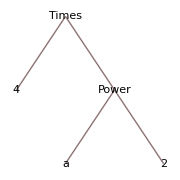

```mathematica
TreeForm[4*a^2]
```

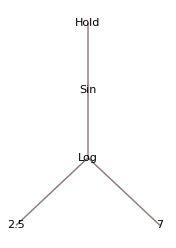

```mathematica
TreeForm[Hold[Sin[Log[2.5,7]]]]
```

## Evaluation process of an expression

The evaluation process in MMA involves the iterative replacement of rules associated with their corresponding symbols until no further rule replacement are possible.

Types of rules

There is 6 types of rules. The symbol with rules is called the rule’s tag.

type of rule | for evaluation of | example
OwnValues[sym] | sym | sym:=
DownValues[sym] | sym[...] | sym[...]:=
UpValues[sym] | head[...sym...] or head[..._sym...] | head[...sym...]^:= or sym /: head[...sym...]:=
SubValues[sym] | sym[...][...] | sym[...][...]:=...
NValues[sym] | N[sym, precision] or N[sym[...],precision] | N[sym[...],precision]:=...
FormatValues[sym] | format[sym[...]] | Format[sym[...],format]:=

In the case of a symbol with OwnValues, the symbol itself will be replaced during evaluation.

```mathematica
a:=b+c
```

```mathematica
OwnValues[a]
```

{HoldPattern[a]:>b+c}

```mathematica
Head[a]
```

Plus